# optical cavity reflection and transmission

P. Huft

Expressions from Mark’s optics notes on Fabry-Perot resonators.

Reproduce Mark’s Fig. 3.6

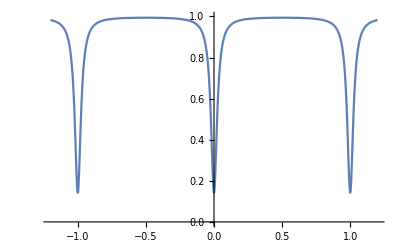

```mathematica
Rin =0.9;
(*Tin = ;*)
Rout = 0.8;
(*Tout = ;*)
Lcav =0.01;
RR = Rin Rout (1-Lcav);
L= 1.5*10^-4;
c=3*10^8;
νFSR = c/(2L);
(*reflected intensity, normalized. assumes IOR n(ν)=1*)
Ir = Rin 1/((1-RR^(1/2))^2+4(RR^(1/2))Sin[π  ν /νFSR]^2)((1-RR^(1/2)/Rin)^2+4(RR^(1/2)/Rin)Sin[π  ν /νFSR]^2);
Plot[Ir/.ν->f νFSR,{f,-1.2,1.2},PlotRange->{0,1}]
```

Fiber cavity

FSR: 1. THz

reflection dip on resonance: 0.0487355

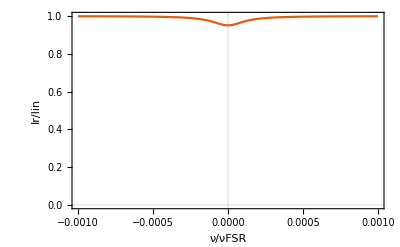

```mathematica
Tin =1600/10^6;
Rin =1-Tin;
Tout =20/10^6;
Rout = 1-Tout;
Lcav =0.0; (*scattering losses, e.g. from mirror clipping the mode*)
RR = Rin Rout (1-Lcav);
L= 1.5*10^-4;
c=3*10^8;
νFSR = c/(2L);
Print["FSR: ",νFSR /10^12," THz"]
(*reflected intensity, normalized. assumes IOR n(ν)=1*)
Ir = Rin 1/((1-RR^(1/2))^2+4(RR^(1/2))Sin[π  ν /νFSR]^2)((1-RR^(1/2)/Rin)^2+4(RR^(1/2)/Rin)Sin[π  ν /νFSR]^2);
Print["reflection dip on resonance: ",1-Ir/.ν->0]
Plot[Ir/.ν->f νFSR,{f,-.001,.001},PlotRange->{0,1},PlotTheme->"Scientific",FrameLabel->{"ν/νFSR","Ir/Iin"}]
```